```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
cm = 72/2.54;
```

```mathematica
plotsDir = "../../../plots/plots-thesis";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data[1] = Import["../../../runs/Trials/N9K9/16602768.dat"];
data[2] = Import["../../../runs/Trials/N9K9/52587911.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
rad[1] = radius/@data[1];
rad[2] = radius/@data[2];
```

```mathematica
fig[1] = Histogram[{rad[1][[All, 2]], rad[2][[All, 2]]}, 350, PDF,
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
FrameLabel->MaTeX/@{"\\Tr X^i X^i", "\\rho"},
FrameTicks->{{With[{ticks=0.0+0.5Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=1.5+0.3Range[0,8]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
ChartLegends->Placed[MaTeX/@{"\\text{a}", "\\text{b}"}, {Bottom, Bottom}],
PlotRange->{{1.5, 3.3}, Automatic},
ImageSize->14cm
];
```

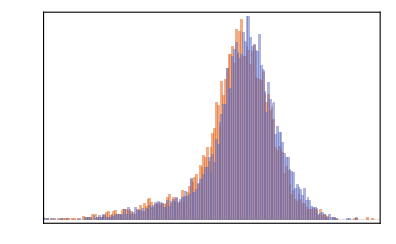

```mathematica
Magnify[fig[1], 1]
```

```mathematica
Export[plotsDir<>"/6-solution-independence.pdf", fig[1]]
```

../../../plots/plots-thesis/6-solution-independence.pdf